```mathematica
pts=Block[
{
positions = example["all particles"],
lastAngle
},
lastAngle = ArcTan@@(positions[[-1]]-positions[[-2]]);
positions = Append[positions,Last[positions]+ AngleVector[lastAngle]];
ifun = Interpolation[MapThread[{#1,#2}&,{Range[Length[positions]],positions}],InterpolationOrder->5];
ifun/@Range[1.2,47.2]
]
```

{{-16.3058,-3.37656},{-16.4892,-2.51436},{-15.94,-1.6587},{-15.1822,-0.98496},{-14.2535,-0.89339},{-13.5154,-1.60563},{-12.6623,-2.15193},{-12.0341,-2.87221},{-11.7763,-3.78677},{-10.9978,-4.37916},{-10.7277,-5.35638},{-10.0659,-6.16162},{-9.23224,-6.30902},{-8.93637,-5.23245},{-8.42957,-4.57315},{-7.49092,-5.07072},{-6.50337,-5.38319},{-5.65893,-5.22724},{-5.44396,-4.20474},{-4.73628,-3.49615},{-3.97281,-2.8778},{-3.87388,-1.89153},{-4.23626,-0.929685},{-4.70587,-0.122377},{-5.73618,-0.126609},{-6.70682,-0.286736},{-7.65591,0.0749321},{-8.57944,0.384345},{-9.39023,-0.177924},{-9.76539,-1.13319},{-10.4985,-1.79061},{-11.3983,-1.49808},{-11.5636,-0.472141},{-11.7609,0.484042},{-12.173,1.41113},{-11.6304,2.09863},{-10.7692,2.0322},{-10.4531,3.02085},{-9.5319,3.43493},{-8.53249,3.51715},{-7.54636,3.63259},{-6.5509,3.94381},{-5.7068,3.94345},{-5.22556,3.05097},{-4.24285,3.13267},{-3.47044,3.73167},{-2.39995,3.45507}}

```mathematica
positions=example["all particles"];
```

```mathematica
pti = pts/@(Range[1,Length[positions]]/Length[positions])
```

{{-16.1017,-1.96271},{-15.3946,-1.21821},{-14.5585,-0.952369},{-13.79,-1.35513},{-13.027,-1.9303},{-12.313,-2.54011},{-11.9289,-3.34631},{-11.3912,-4.04295},{-10.9043,-4.80352},{-10.4701,-5.63644},{-9.77328,-6.18282},{-9.18002,-5.92631},{-8.79963,-5.08959},{-8.19713,-4.7803},{-7.33144,-5.09923},{-6.41432,-5.31466},{-5.72412,-5.03607},{-5.35059,-4.22294},{-4.73327,-3.51739},{-4.10281,-2.8606},{-3.9391,-1.98321},{-4.20696,-1.08419},{-4.66316,-0.333173},{-5.51146,-0.1373},{-6.44716,-0.217791},{-7.36553,-0.0414375},{-8.24426,0.246724},{-9.06789,0.0169431},{-9.60252,-0.713259},{-10.1483,-1.45233},{-10.9362,-1.6194},{-11.4494,-1.02166},{-11.631,-0.0930767},{-11.9186,0.792137},{-11.9586,1.63516},{-11.364,2.01},{-10.7488,2.345},{-10.2285,3.04591},{-9.38196,3.40986},{-8.43702,3.5332},{-7.4925,3.67311},{-6.56325,3.89486},{-5.78255,3.81841},{-5.20344,3.23371},{-4.36825,3.17297},{-3.467,3.54077},{-1.6435,3.49482}}

```mathematica
pts[1]
```

{-1.6435,3.49482}

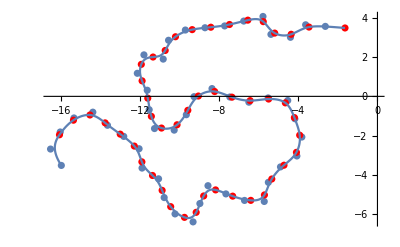

```mathematica
Show[ListPlot[example["all particles"]],
ListPlot[pti,PlotStyle->Red]
,ParametricPlot[pts[t],{t,0,1}]]
```

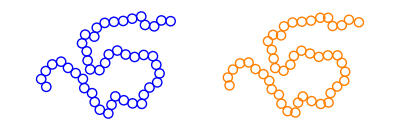

```mathematica
Graphics[
{
Blue,Circle[#,1/2]&/@example["all particles"],
Orange,
Circle[# + {20,0},1/2-.01]&/@pts}]
```

## Start here

```mathematica
p1 = {x0,y0} + {Cos[α],Sin[α]}t
```

{x0+t Cos[α],y0+t Sin[α]}

```mathematica
p2 = {x0,y0} +{Cos[θ],Sin[θ]} + s {Cos[α + β],Sin[α+β]}
```

{x0+s Cos[α+β]+Cos[θ],y0+s Sin[α+β]+Sin[θ]}

```mathematica
sols =Solve[(p2-p1).(p2-p1)==1,s]
```

{{s→1/(2 (Cos[α+β]^2+Sin[α+β]^2))(2 t Cos[α] Cos[α+β]-√2 √(1-t^2+t^2 Cos[2 β]+Cos[2 α+2 β-2 θ]+2 t Cos[α-θ]-2 t Cos[α+2 β-θ])-2 Cos[α+β] Cos[θ]+2 t Sin[α] Sin[α+β]-2 Sin[α+β] Sin[θ])},{s→1/(2 (Cos[α+β]^2+Sin[α+β]^2))(2 t Cos[α] Cos[α+β]+√2 √(1-t^2+t^2 Cos[2 β]+Cos[2 α+2 β-2 θ]+2 t Cos[α-θ]-2 t Cos[α+2 β-θ])-2 Cos[α+β] Cos[θ]+2 t Sin[α] Sin[α+β]-2 Sin[α+β] Sin[θ])}}

```mathematica
Simplify[sols,Assumptions->{0 < α< 2 Pi,0< β< 2Pi, 0 < θ < 2 Pi}]
```

{{s→t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+2 t Cos[α-θ]+Cos[2 (α+β-θ)]-2 t Cos[α+2 β-θ]))/(√2)},{s→t Cos[β]-Cos[α+β-θ]+(√(1-t^2+t^2 Cos[2 β]+2 t Cos[α-θ]+Cos[2 (α+β-θ)]-2 t Cos[α+2 β-θ]))/(√2)}}

```mathematica
tmp=Simplify[sols/.t->0,Assumptions->{0 < α< 2 Pi,0< β< θ < 2Pi}]
```

{{s→-Abs[Cos[α+β-θ]]-Cos[α+β-θ]},{s→Abs[Cos[α+β-θ]]-Cos[α+β-θ]}}

```mathematica
Simplify[tmp,Assumptions->Cos[β-θ]>0]
```

{{s→-Abs[Cos[α+β-θ]]-Cos[α+β-θ]},{s→Abs[Cos[α+β-θ]]-Cos[α+β-θ]}}

```mathematica
Simplify[tmp,Assumptions->Cos[β-θ]<0]
```

{{s→-Abs[Cos[α+β-θ]]-Cos[α+β-θ]},{s→Abs[Cos[α+β-θ]]-Cos[α+β-θ]}}

```mathematica
Simplify[sols/.t->0,Assumptions->{0 < α< 2 Pi,0< β< 2Pi, 0 < θ < 2 Pi}]
```

{{s→-Abs[Cos[α+β-θ]]-Cos[α+β-θ]},{s→Abs[Cos[α+β-θ]]-Cos[α+β-θ]}}

```mathematica
sols =FullSimplify[sols, Assumptions->{0 < α< 2 Pi,0< β< θ < 2Pi}]
```

{{s→t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)},{s→t Cos[β]-Cos[α+β-θ]+(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)}}

```mathematica
sSols = s/.FullSimplify[sols, Assumptions->{0 < α< 2 Pi,0< β< θ < 2Pi}]
```

{t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2),t Cos[β]-Cos[α+β-θ]+(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)}

```mathematica
Simplify[(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ])/.t->0,Assumptions->{0 < α< 2 Pi,0< β< θ < 2Pi}]
```

2 Cos[α+β-θ]^2

```mathematica
p2NextSols=FullSimplify[p2/.sols,Assumptions->{0 < α< 2 Pi,0< β< 2Pi, 0 < θ < 2 Pi}]
```

{{x0+Cos[θ]+Cos[α+β] (t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)),y0+Sin[α+β] (t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2))+Sin[θ]},{x0+Cos[θ]+Cos[α+β] (t Cos[β]-Cos[α+β-θ]+(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)),y0+Sin[α+β] (t Cos[β]-Cos[α+β-θ]+(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2))+Sin[θ]}}

```mathematica
p2NextSol=FullSimplify[p2/.sols[[1]],Assumptions->{0 < α< 2 Pi,0< β< 2Pi, 0 < θ < 2 Pi}]
```

{x0+Cos[θ]+Cos[α+β] (t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)),y0+Sin[α+β] (t Cos[β]-Cos[α+β-θ]-(√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2))+Sin[θ]}

```mathematica
Manipulate[
Plot[1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ],{t,0,1},PlotRange->{0,1}],
{θ,0,2Pi},
{α,0,2 Pi},
{β,0,2 Pi}

]
```

```mathematica
tLimits =t/.Solve[1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]==0,t]
```

{Csc[β] (-1+Sin[α+β-θ]),Csc[β] (1+Sin[α+β-θ])}

```mathematica
Manipulate[{Csc[β] (-1+Sin[α+β-θ]),Csc[β] (1+Sin[α+β-θ])},{θ,0,2Pi},
{α,0,2 Pi},
{β,0,2 Pi}]
```

```mathematica
tMax[θ_,α_,β_]:=If[PossibleZeroQ[β],1,Min[{Max[ {Csc[β] (-1+Sin[α+β-θ]),Csc[β] (1+Sin[α+β-θ])}],1}]]
```

```mathematica
p2NextPosition[{x0_,y0_},θ_,α_,β_,t_]:= Block[{root = (√(1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]))/(√2)},
{   x0+Cos[θ]+Cos[α+β] (t Cos[β]-Cos[α+β-θ]- root),
y0+Sin[θ]+ Sin[α+β] (t Cos[β]-Cos[α+β-θ]-root)}]
```

```mathematica
With[{p1 = p1/.{x0->0,y0->0},sSols=sSols },
Manipulate[Graphics[{Blue,Disk[p1,1/2],Circle[{0,0},1/2],Orange,Disk[p2NextPosition[{0,0},θ,α,β,t],1/2],Circle[p2NextPosition[{0,0},θ,α,β,0],1/2],
Black,Line[{{0,0}, AngleVector[α]}]
(*,Line[{p2NextPosition[{0,0},θ,α,β,0],p2NextPosition[{0,0},θ,α,β,tMax[θ,α,β]]}]*)
}, PlotRange->3{{-1,1},{-1,1}}],
{θ,0,2Pi},
{α,0,2 Pi},
{β,0,2 Pi},
{t,0,1},
Dynamic[1-t^2+t^2 Cos[2 β]+Cos[2 (α+β-θ)]+4 t Sin[β] Sin[α+β-θ]],
Dynamic[{Csc[β] (-1+Sin[α+β-θ]),Csc[β] (1+Sin[α+β-θ])}],
Dynamic[tMax[θ,α,β]],
Dynamic[sSols]
]
]
```

## Numerical Solution (George)

Consider a particle at (0,0) and another at (Cos[θ],Sin[θ])

Move first particle at an angle α at rate 1

```mathematica
differentialEqs={
x[2]'[t]==(λ[2][t]) (x[2][t]-Cos[α]t), 
y[2]'[t]==(λ[2][t]) (y[2][t]-Sin[α]t)
};

algebraicEqs={
(x[2][t]-Cos[α]t)^2+(y[2][t]-Sin[α]t)^2==1
};

initialConds[θ_]={
x[2][0]==Cos[θ],y[2][0]==Sin[θ]
};
```

Numerical Solution

```mathematica
parametricNumericalSolution=ParametricNDSolveValue[{differentialEqs,algebraicEqs,initialConds[θ]},{x[2],y[2],λ[2]},{t,0,10},{α,θ},Method->{"IndexReduction"->{Automatic,"IndexGoal"->0}}]
```

ParametricFunction[<>]

Visualize Solution

```mathematica
visualizeDimer[α_,θ_][x2_,y2_][t_]:=
Graphics[{
{Red,Dashed,Arrow[{{0,0},5AngleVector[α]}],Circle[{0,0},1/2],Disk[{Cos[α]t,Sin[α]t},1/2]},
{Blue,Dashed,Circle[AngleVector[θ],1/2],Disk[{x2[t],y2[t]},1/2]}
},PlotRange->5{{-1,1},{-1,1}}]
```

```mathematica
frames=With[{f=visualizeDimer[π/4,-π/3][#1,#2]&@@parametricNumericalSolution[π/4,-π/3]},
f/@Subdivide[0,10,100]];
```

```mathematica
Export["rigid-dimer-motion.gif",frames]
```

rigid-dimer-motion.gif

```mathematica
Manipulate[
DynamicModule[{f=visualizeDimer[α,θ][#1,#2]&@@parametricNumericalSolution[α,θ]},
Animate[f[t],{{t,0,"Time"},0,10},AnimationRunning->False,Paneled->False]
],
{{α,π/4,"Angle of Motion"},-π,π},{{θ,-π/3,"Initial Angle of Second Particle"},-π,π},Paneled->False]
```

Eyeballing β -> α

```mathematica
angleDifference[α_,θ_]:=With[{f=parametricNumericalSolution[α,θ]},
ListLinePlot[Table[{t,VectorAngle[AngleVector[α]t,{#1[t],#2[t]}&@@f]},{t,Rest@Subdivide[0,10,250]}],PlotRange->{0,π},Frame->True,FrameTicks->None,ImageSize->200,Epilog->{Text[StringTemplate["α=`1`\nθ=`2`"][α,θ],{7.5,3π/4}]}]
]
```

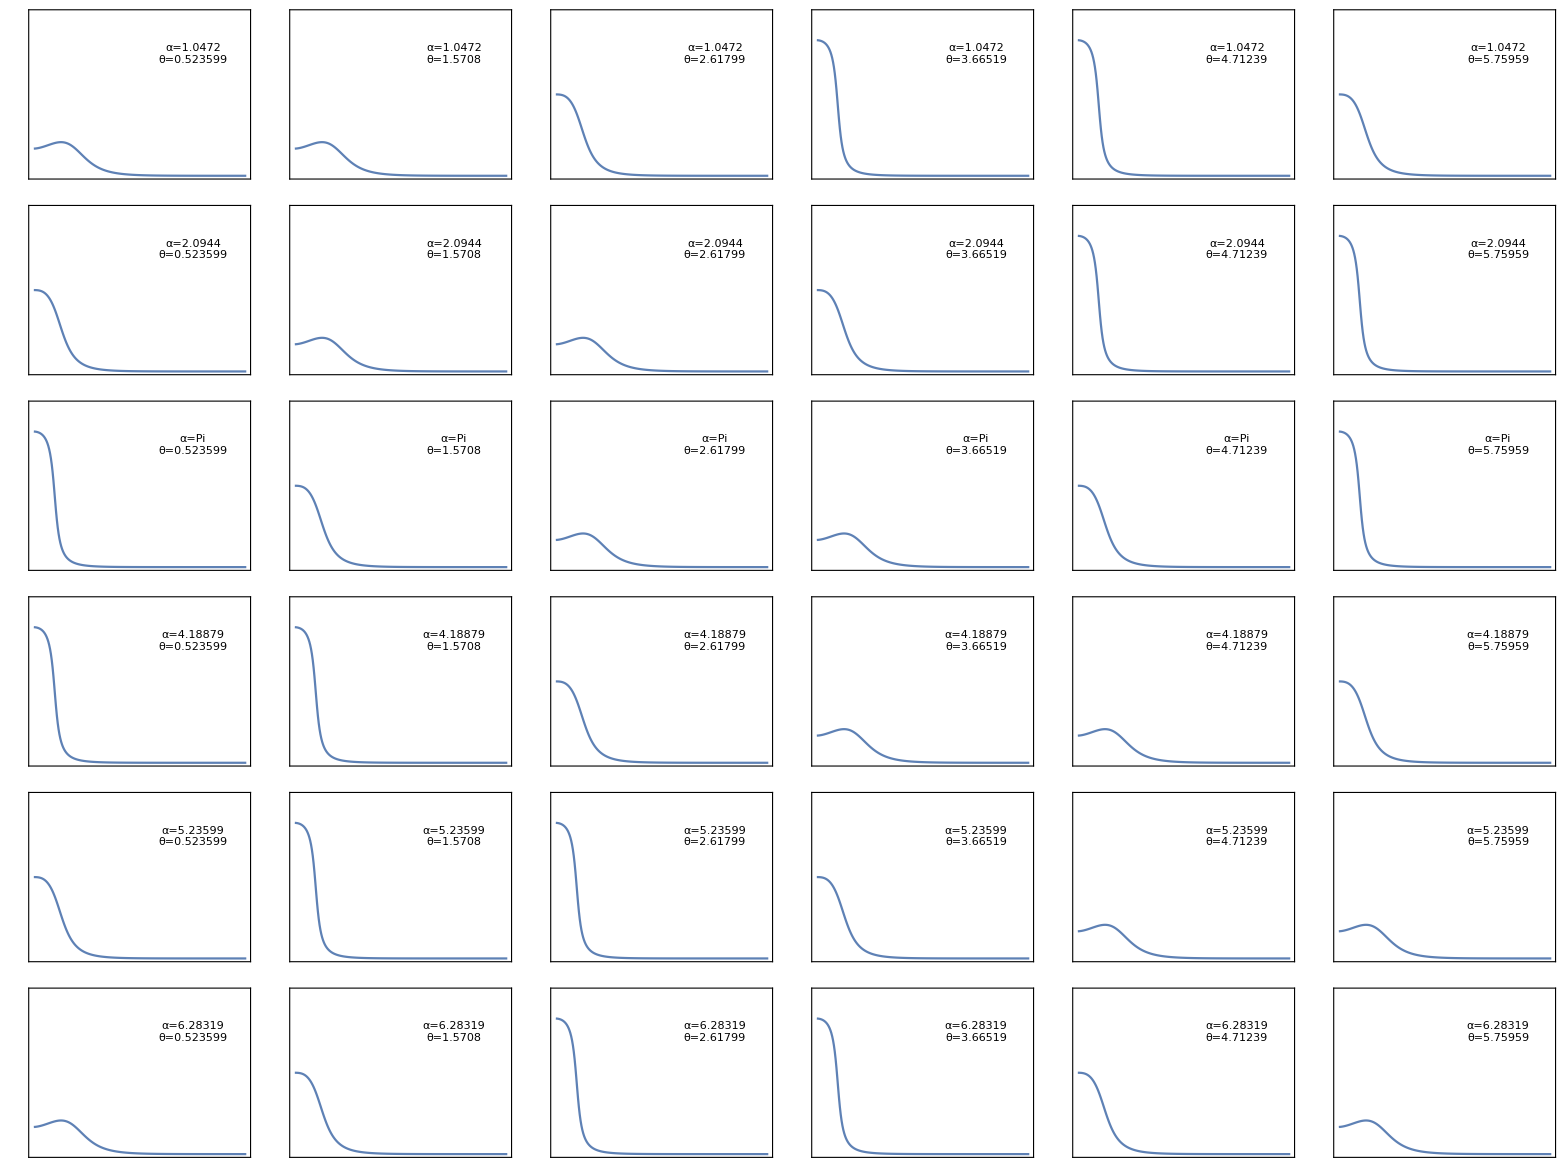

```mathematica
Table[angleDifference[α,θ],{α,Rest@Subdivide[0,2π,6]},{θ,Rest@Subdivide[0,2π,6]-π/6}]//Grid
```